```mathematica
Manipulate[
Plot[
{
BesselJ[0,x],
Sin[s x^0.9515]/x^0.6,
Sinc[s x^e](1+x/2)^0.5(*(1+Log[4,1+x/2])*)
},
{x,-1,40},
PlotStyle->{Green,{Dashed,Red},Purple},
PlotRange->All,
ImageSize->750
],
{s,1.21,5},
{e,0.9505,1.5}
]
```

```mathematica
D[(y-BesselJ[0,s x+c])^2,x]
```

2 s (y-BesselJ[0,c+s x]) BesselJ[1,c+s x]

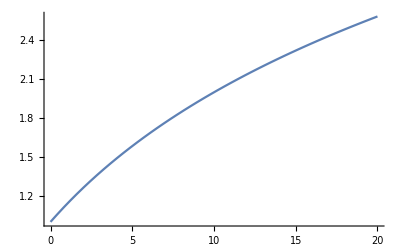

```mathematica
Plot[(1+Log[2,1+x/10]),{x,0,20},
AxesOrigin->{0,0},
PlotRange->All]
```